# End Semester Project

## Author Identification

## Submitted by : Shubhang Periwal Student Id: 19201104

## Introduction:

### Author Identification:

Authorship identification is the task of identifying the author of a given text from a set of suspects. It is an emerging area of research associated with applications in literary research, cyber-security, forensics, and social media analysis. So, given some amount of text (5-7 words), the given classifier will be able to identify the author of that text. The more amount of text we present it, the more accurate the result becomes. This is to show that each and every author (mostly) have a unique style of writing text, from which we can back-trace it back to the author. For example William Shakespeare has a different writing style when compared to the style of Augusta Christine or any other author.

### Dataset:

The dataset are actual text by the authors William Shakespeare, Sir Arthur Conan Doyle and JK Rowling. I have used some part of text for each of the authors. For example I used 1 part of Harry Potter (out of the 8 parts ), some small texts by William Shakespeare and some short Sherlock Holmes stories by Sir Arthur Conan Doyle. The total text accumulated is of around 400 thousand words, but due to computational limitations only 200000 words will be used to train, segregate and identify the author.

### Classifiers:

#### The list of classifiers used are specified below :

Naive Bayes Classifier

Naive Bayes classifiers, a family of classifiers that are based on the popular Bayes’ probability theorem, are known for creating simple yet well performing models, especially in the fields of document classification. 
 Under this naive assumption, the class-conditional probabilities or (likelihoods) of the samples can be directly estimated from the training data instead of evaluating all possibilities of x. Thus, given a d-dimensional feature vector x, the class conditional probability can be calculated as follows:
 -Graphics-
 Here, P(x∣ωj) simply means: “How likely is it to observe this particular pattern x given that it belongs to class ωj?” The “individual” likelihoods for every feature in the feature vector can be estimated via the maximum-likelihood estimate, which is simply a frequency in the case of categorical data:
 -Graphics-
 Nxi,ωj: Number of times feature xi appears in samples from class ωj.
Nωj: Total count of all features in class ωj.

Markov Classifier

A Markov model is a stochastic method for randomly changing systems where it is assumed that future states do not depend on past states. These models show all possible states as well as the transitions, rate of transitions and probabilities between them.

Decision Tree Classifier

A Decision Tree is a simple representation for classifying examples. It is a Supervised Machine Learning where the data is continuously split according to a certain parameter.
Decision Tree consists of :
Nodes : Test for the value of a certain attribute.
Edges/ Branch : Correspond to the outcome of a test and connect to the next node or leaf.
Leaf nodes : Terminal nodes that predict the outcome (represent class labels or class distribution).

Nearest Neighbors Classifier

KNN is a non-parametric, lazy learning algorithm. Its purpose is to use a database in which the data points are separated into several classes to predict the classification of a new sample point. A k-nearest-neighbor algorithm, often abbreviated knn, is an approach to data classification that estimates how likely a data point is to be a member of one group or the other depending on what group the data points nearest to it are in.
The parameters in this model are the distance function, and k. The latter is chosen by training on different values of k, and picking the best one. The distance is often chosen to be the euclidean distance
 			D_(x_1,x_2)=√((x_(1_1)-x_(2_1))^2+(x_(1_2)-x_(2_2))^2+(x_(1_3)-x_(2_3))^2......(x_(1_n)-x_(2_n))^2)

LSTM (Neural Network )

Long short-term memory (LSTM) is an artificial recurrent neural network (RNN) architecture used in the field of deep learning. Unlike standard feedforward neural networks, LSTM has feedback connections. It can not only process single data points (such as images), but also entire sequences of data (such as speech or video). For example, LSTM is applicable to tasks such as unsegmented, connected handwriting recognition, speech recognition and anomaly detection in network traffic or IDS’s (intrusion detection systems).

Gradient Boosted Trees Classifier

Gradient boosting is a machine learning technique for regression and classification problems, which produces a prediction model in the form of an ensemble of weak prediction models, typically decision trees. It builds the model in a stage-wise fashion like other boosting methods do, and it generalizes them by allowing optimization of an arbitrary differentiable loss function.

CNN (Convolution neural network for text classification)

A Convolutional Neural Network typically involves two operations, which can be though of as feature extractors: convolution and pooling.
In the case of NLP tasks, i.e., when applied to text instead of images, we have a 1 dimensional array representing the text. Here the architecture of the ConvNets is changed to 1D convolutional-and-pooling operations.
One of the most typically tasks in NLP where ConvNet are used is sentence classification, that is, classifying a sentence into a set of pre-determined categories by considering n-grams, i.e. it’s words or sequence of words, or also characters or sequence of characters.

## Code:

#### Data Pre-processing:

```mathematica
SetDirectory["C:\\Users\\shubh\\OneDrive\\Desktop\\dataset"];
shakespeareFiles=FileNames["*.txt","C:\\Users\\shubh\\OneDrive\\Desktop\\dataset\\shakespeare"];
shakespeareText = Map[Import,shakespeareFiles[[1;;10]]];
Length[shakespeareText];
arthurFiles = FileNames["*.txt","C:\\Users\\shubh\\OneDrive\\Desktop\\dataset\\arthur"];
arthurText = Map[Import,arthurFiles];
jkrowFiles = FileNames["*.txt","C:\\Users\\shubh\\OneDrive\\Desktop\\dataset\\jkrow"];
jkrowText = Map[Import,jkrowFiles];
```

Kindly set the directory accordingly. Place the dataset folder within and leave the rest. The above functions import the entire text present within the files and convert them into pure text file.

```mathematica
shakespeareText
```

{	1 KING HENRY IV


	DRAMATIS PERSONAE


KING HENRY	the Fourth. (KING HENRY IV:)


HENRY,
Prince of Wales	(PRINCE HENRY:)	|
		| sons of the King
JOHN of Lancaster	(LANCASTER:)	|


WESTMORELAND:

SIR WALTER BLUNT:

THOMAS PERCY	Earl of Worcester. (EARL OF WORCESTER:)

HENRY PERCY	Earl of Northumberland. (NORTHUMBERLAND:)

HENRY PERCY	surnamed HOTSPUR, his son.… meet Northumberland and the prelate Scroop,
	Who, as we hear, are busily in arms:
	Myself and you, son Harry, will towards Wales,
	To fight with Glendower and the Earl of March.
	Rebellion in this land shall lose his sway,
	Meeting the cheque of such another day:
	And since this business so fair is done,
	Let us not leave till all our own be won.

	[Exeunt],8,…}
 |  |  |  |

Above, you can see sample of the kind of text that I am getting once extracted from files.

```mathematica
punctuation=Alternatives@@Characters[",.?:;'\"!-"];
glove = NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"];
```

GloVe is an unsupervised learning algorithm for obtaining vector representations for words. Training is performed on aggregated global word-word co-occurrence statistics from a corpus, and the resulting representations showcase interesting linear substructures of the word vector space. In the above case it converts each and every word to a 100 dimensional vector in 100D space.

```mathematica
arthurTextBpp = DeleteStopwords[StringJoin[arthurText]];
shakespeareBpp = DeleteStopwords[StringJoin[shakespeareText]];
jkrowTextBpp = DeleteStopwords[StringJoin[jkrowText]];

arthurTextBpp = StringReplace[arthurTextBpp,PunctuationCharacter:>" "];
shakespeareBpp= StringReplace[shakespeareBpp,PunctuationCharacter:>" "];
jkrowTextBpp = StringReplace[jkrowTextBpp,PunctuationCharacter:>" "];

arthurTextBpp = StringJoin[StringCases[arthurTextBpp,RegularExpression["[a-z]|[A-Z]|\\s"]]];
shakespeareBpp= StringJoin[StringCases[shakespeareBpp,RegularExpression["[a-z]|[A-Z]|\\s"]]];
jkrowTextBpp = StringJoin[StringCases[jkrowTextBpp,RegularExpression["[a-z]|[A-Z]|\\s"]]];

arthurTextBpp = StringSplit[arthurTextBpp];
shakespeareBpp = StringSplit[shakespeareBpp];
jkrowTextBpp = StringSplit[jkrowTextBpp ];
```

Firstly, we are removing stop-words (commonly occurring words such as ‘the’,’a’ and a couple of more prepositions ). We need to remove this as to separate out noise from the text.  We further remove punctuation characters (though useful, but better if separated). We further use regular expressions to clean the data and remove any additional unwanted data.

```mathematica
arthur$dataGl = Map[# -> "arthur" &,glove[WordStem[arthurTextBpp]]//.{x_}:>x];
jkrow$dataGl =  Map[# -> "jkrow" &,glove[WordStem[jkrowTextBpp]]//.{x_}:>x];
shakes$dataGl = Map[# -> "shakes" &,glove[WordStem[shakespeareBpp]]//.{x_}:>x];

arthurmap = Map[#->"arthur"&,arthurTextBpp//WordStem];
jkrowmap = Map[#->"jkrow"&,jkrowTextBpp//WordStem];
shakespearemap = Map[# -> "shakes"&,shakespeareBpp//WordStem];
```

We need to map the data and assign it the class that we need. In the first case we are using glove function to convert the data into vector form and removing a set of brackets as glove assigns a set of brackets(returns a list, then it would have been a list of list). The names of the classes are “arthur”, “jkrow” and “shakes”. We are here using the stemmed part of the word which ignores the plural and other forms(future tense, past tense etc) of a word and generates a stem of the word.
 Stemming is basically removing the suffix from a word and reduce it to its root word. For example: “Flying” is a word and its suffix is “ing”, if we remove “ing” from “Flying” then we will get base word or root word which is “Fly”.

```mathematica
data = Join[arthurmap,jkrowmap,shakespearemap];
data = RandomSample[data];
dataGl = Join[arthur$dataGl,jkrow$dataGl,shakes$dataGl]//RandomSample;
arthur$dataGlNN = Map[# -> "arthur" &,glove[arthurTextBpp]];
jkrow$dataGlNN =  Map[# -> "jkrow" &,glove[jkrowTextBpp]];
shakes$dataGlNN = Map[# -> "shakes" &,glove[shakespeareBpp]];
dataGlNN = Join[arthur$dataGlNN,jkrow$dataGlNN,shakes$dataGlNN]//RandomSample;
```

We then join the datasets into a data variable and perform a random sample so as to shuffle the data inorder to have better training. We need to have a slight different dataset for input in the neural network.

```mathematica
trainingData = data[[1;;200000]];
testData = data[[200001;;210000]];
trainingDataGl= dataGl[[1;;200000]];
testDataGl = dataGl[[200001;;210000]];
trainingDataGlNN = dataGlNN[[1;;200000]];
testDataGlNN = dataGlNN[[200001;;210000]];
arthurTextBpp//Length
shakespeareBpp//Length
jkrowTextBpp//Length
```

103673

127518

134175

We create a training and a testing set for the data. I should’ve taken more text for both Sir Arthur Conan Doyle and JK Rowling but I would not be able to perform training due to computational limitations.

#### Classifiers:

I have exported all the classifiers so that we do not need to train the data again and again. All the classifiers are the the dataset folder.

```mathematica
naivebayesClassifier=Classify[trainingData,Method->"NaiveBayes"]
```

ClassifierFunction[…]

```mathematica
Export["naivebayesClassifier.wmlf",naivebayesClassifier]
```

naivebayesClassifier.wmlf

```mathematica
naivebayesClassifier= Import["naivebayesClassifier.wmlf"]
```

ClassifierFunction[…]

```mathematica
DecisionTreeClassifier = Classify[trainingData,Method->"DecisionTree"]
```

ClassifierFunction[…]

```mathematica
Export["DecisionTreeClassifier.wmlf",DecisionTreeClassifier]
```

DecisionTreeClassifier.wmlf

```mathematica
DecisionTreeClassifier = Import["DecisionTreeClassifier.wmlf"]
```

ClassifierFunction[…]

```mathematica
MarkovClassifier = Classify[trainingData,Method->"Markov"]
```

ClassifierFunction[…]

```mathematica
Export["MarkovClassifier.wmlf",MarkovClassifier]
```

MarkovClassifier.wmlf

```mathematica
MarkovClassifier = Import["MarkovClassifier.wmlf"]
```

ClassifierFunction[…]

```mathematica
GradientBoostedTreesClassifier = Classify[trainingData,Method->"GradientBoostedTrees"]
```

ClassifierFunction[…]

```mathematica
Export["GradientBoostedTreesClassifier.wmlf",GradientBoostedTreesClassifier]
```

GradientBoostedTreesClassifier.wmlf

```mathematica
GradientBoostedTreesClassifier = Import["GradientBoostedTreesClassifier.wmlf"]
```

ClassifierFunction[…]

```mathematica
NearestNeighborsClassifier = Classify[trainingData,Method->{"NearestNeighbors","NeighborsNumber"->5}]
```

ClassifierFunction[…]

```mathematica
Export["NearestNeighborsClassifier.wmlf",NearestNeighborsClassifier]
```

NearestNeighborsClassifier.wmlf

```mathematica
NearestNeighborsClassifier= Import["NearestNeighborsClassifier.wmlf"]
```

ClassifierFunction[…]

```mathematica
Classifier = Classify[trainingData]
```

ClassifierFunction[…]

```mathematica
Export["Classifier.wmlf",Classifier]
```

Classifier.wmlf

```mathematica
Classifier= Import["Classifier.wmlf"]
```

ClassifierFunction[…]

```mathematica
net=NetChain[{EmbeddingLayer[40],DropoutLayer[0.1],LongShortTermMemoryLayer[20],SequenceLastLayer[],LinearLayer[3],SoftmaxLayer[]},"Input"->NetEncoder[{"Tokens"}],"Output"->NetDecoder[{"Class",{"arthur","jkrow","shakes"}}]]
result=NetTrain[net,trainingData,All,ValidationSet->testData,MaxTrainingRounds->5,TargetDevice->"GPU"]
trained=result["TrainedNet"]
```

NetChain[<>]

NetTrain Results
summary | ,,  batches:31250  rounds:5  time:2.2min  examples/s:7492
data | ,,  training examples:200000  validation examples:10000  processed examples:1000000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32GPU
round | ,,  loss:9.03×10^-1  error:46.7%
validation | ,,  loss:9.3×10^-1  error:48.5%
 | 
-Graphics-  training set	-Graphics-  validation set |

NetChain[<>]

```mathematica
Export["trained.wmlf",trained]
```

trained.wmlf

```mathematica
trained= Import["trained.wmlf"]
```

NetChain[<>]

The above network is a 6 layered neural network which input type as string and output type as one of the class as mentioned in the NetDecoder. The input is a list of tokens(stemmed words). 
Neural network embeddings have 3 primary purposes:
Finding nearest neighbors in the embedding space. These can be used to make recommendations based on user interests or cluster categories.
As input to a machine learning model for a supervised task.
For visualization of concepts and relations between categories.
I have added a dropout layer so as to prevent overfitting of the model. This drops out some of the training samples proportional to the value inside. 
LSTM(Long short term memory)
-Graphics-
It is a self feedback loop layer after a particular timestamp. In above case the value of the timestamp is 20. 
Then there is a sequence layer followed by a final decoding or linear layer which finally does the classification. 
We need to have GPU installed for the same or you could try it on your pc by reducing the size of the training set.

The second set of classifiers which use Glove features

```mathematica
DecisionTreeClassifierGl = Classify[trainingDataGl,Method->"DecisionTree"]
```

ClassifierFunction[…]

```mathematica
Export["DecisionTreeClassifierGl.wmlf",DecisionTreeClassifierGl]
```

DecisionTreeClassifierGl.wmlf

```mathematica
DecisionTreeClassifierGl= Import["DecisionTreeClassifierGl.wmlf"]
```

ClassifierFunction[…]

```mathematica
GradientBoostedTreesClassifierGl = Classify[trainingDataGl,Method->"GradientBoostedTrees"]
```

ClassifierFunction[…]

```mathematica
Export["GradientBoostedTreesClassifierGl.wmlf",GradientBoostedTreesClassifierGl]
```

GradientBoostedTreesClassifierGl.wmlf

```mathematica
GradientBoostedTreesClassifierGl= Import["GradientBoostedTreesClassifierGl.wmlf"]
```

ClassifierFunction[…]

```mathematica
NearestNeighborsClassifierGl = Classify[trainingDataGl,Method->{"NearestNeighbors","NeighborsNumber"->5}]
```

ClassifierFunction[…]

```mathematica
Export["NearestNeighborsClassifierGl.wmlf",NearestNeighborsClassifierGl]
```

NearestNeighborsClassifierGl.wmlf

```mathematica
NearestNeighborsClassifierGl= Import["NearestNeighborsClassifierGl.wmlf"]
```

ClassifierFunction[…]

```mathematica
net2=NetChain[{ConvolutionLayer[100,1],Ramp,PoolingLayer[16,1],ConvolutionLayer[50,1],Ramp,PoolingLayer[4,1],FlattenLayer[],500,Ramp,3,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",{"arthur","jkrow","shakes"}}],"Input"->{1,100}]
result2=NetTrain[net2,trainingDataGlNN,All,ValidationSet->testDataGlNN,MaxTrainingRounds->5,TargetDevice->"GPU"]
```

```mathematica
trained2=result2["TrainedNet"]
```

NetChain[<>]

```mathematica
Export["trained2.wmlf",trained2]
```

trained2.wmlf

```mathematica
trained2= Import["trained2.wmlf"]
```

NetChain[<>]

This is the second neural network. This is a convolution neural network which takes in an input vector of dimensions 100 by 1 (as resulted by the glove model), this is followed by a pooling layer which pools the data to the size of 16. This is followed by another convolution layer and pooling layer to flatten the data. The final output is of the size 3 which consists of a net decoder to finally decode the output. The number of training rounds is 5 and the target device is set as GPU.

```mathematica
ClassifierGl = Classify[trainingDataGl]
```

ClassifierFunction[…]

```mathematica
Export["ClassifierGl.wmlf",ClassifierGl ]
```

ClassifierGl.wmlf

```mathematica
ClassifierGl = Import["ClassifierGl.wmlf"]
```

ClassifierFunction[…]

This is the inbuilt classifier which uses the best among all the classifiers.

#### Testing of the classifiers:

```mathematica
arthurtest = {};jkrowtest = {};shakestest={};
For[i=210000,i<250000,i++,Switch[data[[i]][[2]],"arthur",arthurtest = Append[arthurtest,data[[i]][[1]]],
"jkrow", jkrowtest = Append[jkrowtest,data[[i]][[1]]],"shakes",shakestest = Append[shakestest,data[[i]][[1]]]]]
```

Here I am creating the final mapped set for creating subsequences of multiple and different sizes

```mathematica
arthurtestFinal = {};
shakestestFinal = {};
jkrowtestFinal = {};
count = 1;
len = (arthurtest//Length) - 20;
While[count < len,temp = RandomInteger[{5,7}];
arthurtestFinal = Join[arthurtestFinal,List[arthurtest[[count;;count+temp]]]];count = count + temp;]
len = (shakestest//Length) - 20;
count = 1;
While[count < len,temp = RandomInteger[{5,7}];
shakestestFinal = Join[shakestestFinal ,List[shakestest[[count;;count+temp]]]];count = count + temp;]
len = (jkrowtest//Length) - 20;
count = 1;
While[count < len,temp = RandomInteger[{5,7}];
jkrowtestFinal = Join[jkrowtestFinal,List[jkrowtest [[count;;count+temp]]]];count = count + temp;]
```

Here I am creating a final test subset, getting sequences of random lengths between 5 and 7 to  test against all trained models.  
I have used the first 210000 for training and validation, so would be using the remaining words for the final testing.

```mathematica
classer = Function[{x,y}, poll={0,0,0};result ={0,0,0}; count = Length[x];
For[i=1,i<=count,i = i+1,
For[j=1,j<=Length[x[[i]]],j = j+1,
z = x[[i]][[j]];
res = ToString[y[ToString[z]]];

Switch[res,"jkrow",poll[[2]]= poll[[2]]+1,"arthur",poll[[3]]= poll[[3]]+1,"shakes",poll[[1]]= poll[[1]]+1];
];
result[[PositionIndex[poll][Max[poll]][[1]]]]=result[[PositionIndex[poll][Max[poll]][[1]]]]+1;

poll={0,0,0};
];Return[result];];

classer2 = Function[{x,y}, poll={0,0,0};result ={0,0,0}; count = Length[x];
For[i=1,i<=count,i = i+1,
For[j=1,j<=Length[x[[i]]],j = j+1,
z = x[[i]][[j]];
res = y[glove[z]];
res = res//.{u_}:>u;

Switch[res,"jkrow",poll[[2]]= poll[[2]]+1,"arthur",poll[[3]]= poll[[3]]+1,"shakes",poll[[1]]= poll[[1]]+1];

];
result[[PositionIndex[poll][Max[poll]][[1]]]]=result[[PositionIndex[poll][Max[poll]][[1]]]]+1;


poll={0,0,0};
];Return[result];];
```

The classer function above takes input the dataset and the name of the classifier as its parameters and returns the resultant array of classified data. 
Classer2 performs the same function as classer but it is meant for classifiers that use glove input.

```mathematica
resultArthur = {"Result Arthur"};
resultArthur = Append[resultArthur,classer[arthurtestFinal[[1;;100]],MarkovClassifier][[1]]];
resultArthur= Append[resultArthur,classer[arthurtestFinal[[1;;100]],naivebayesClassifier][[1]]];
resultArthur = Append[resultArthur,classer[arthurtestFinal[[1;;100]],DecisionTreeClassifier][[1]]];
resultArthur = Append[resultArthur,classer[arthurtestFinal[[1;;100]],GradientBoostedTreesClassifier][[1]]];
resultArthur= Append[resultArthur,classer[arthurtestFinal[[1;;100]],NearestNeighborsClassifier ][[1]]];
resultArthur = Append[resultArthur,classer[arthurtestFinal[[1;;100]],Classifier][[1]]];
resultArthur= Append[resultArthur,classer[arthurtestFinal[[1;;100]],trained][[1]]];
resultArthur = Append[resultArthur,classer2[arthurtestFinal[[1;;100]],DecisionTreeClassifierGl][[1]]];
resultArthur = Append[resultArthur,classer2[arthurtestFinal[[1;;100]],GradientBoostedTreesClassifierGl ][[1]]];
resultArthur= Append[resultArthur,classer2[arthurtestFinal[[1;;100]],NearestNeighborsClassifierGl][[1]]];
resultArthur= Append[resultArthur,classer2[arthurtestFinal[[1;;100]],trained2][[1]]];
resultArthur= Append[resultArthur,classer2[arthurtestFinal[[1;;100]],ClassifierGl][[1]]];

resultShakes = {"Result Shakes"};
resultShakes = Append[resultShakes,classer[shakestestFinal[[1;;100]],MarkovClassifier][[1]]];
resultShakes= Append[resultShakes,classer[shakestestFinal[[1;;100]],naivebayesClassifier][[1]]];
resultShakes = Append[resultShakes,classer[shakestestFinal[[1;;100]],DecisionTreeClassifier][[1]]];
resultShakes = Append[resultShakes,classer[shakestestFinal[[1;;100]],GradientBoostedTreesClassifier][[1]]];
resultShakes= Append[resultShakes,classer[shakestestFinal[[1;;100]],NearestNeighborsClassifier ][[1]]];
resultShakes= Append[resultShakes,classer[shakestestFinal[[1;;100]],Classifier][[1]]];
resultShakes= Append[resultShakes,classer[shakestestFinal[[1;;100]],trained][[1]]];
resultShakes = Append[resultShakes,classer2[shakestestFinal[[1;;100]],DecisionTreeClassifierGl][[1]]];
resultShakes = Append[resultShakes,classer2[shakestestFinal[[1;;100]],GradientBoostedTreesClassifierGl ][[1]]];
resultShakes= Append[resultShakes,classer2[shakestestFinal[[1;;100]],NearestNeighborsClassifierGl][[1]]];
resultShakes= Append[resultShakes,classer2[shakestestFinal[[1;;100]],trained2][[1]]];
resultShakes= Append[resultShakes,classer2[shakestestFinal[[1;;100]],ClassifierGl][[1]]];

resultJKrow = {"Result JKrow"};
resultJKrow=Append[resultJKrow,classer[jkrowtestFinal[[1;;100]],MarkovClassifier][[1]]];
resultJKrow=Append[resultJKrow,classer[jkrowtestFinal[[1;;100]],naivebayesClassifier][[1]]];
resultJKrow=Append[resultJKrow,classer[jkrowtestFinal[[1;;100]],DecisionTreeClassifier][[1]]];
resultJKrow=Append[resultJKrow,classer[jkrowtestFinal[[1;;100]],GradientBoostedTreesClassifier][[1]]];
resultJKrow=Append[resultJKrow,classer[jkrowtestFinal[[1;;100]],NearestNeighborsClassifier][[1]]];
resultJKrow=Append[resultJKrow,classer[jkrowtestFinal[[1;;100]],Classifier][[1]]];
resultJKrow=Append[resultJKrow,classer[jkrowtestFinal[[1;;100]],trained][[1]]];
resultJKrow=Append[resultJKrow,classer2[jkrowtestFinal[[1;;100]],DecisionTreeClassifierGl][[1]]];
resultJKrow=Append[resultJKrow,classer2[jkrowtestFinal[[1;;100]],GradientBoostedTreesClassifierGl][[1]]];
resultJKrow=Append[resultJKrow,classer2[jkrowtestFinal[[1;;100]],NearestNeighborsClassifierGl][[1]]];
resultJKrow=Append[resultJKrow,classer2[jkrowtestFinal[[1;;100]],trained2][[1]]];
resultJKrow=Append[resultJKrow,classer2[jkrowtestFinal[[1;;100]],ClassifierGl][[1]]];
```

```mathematica
classifierList = {"Markov","NaiveBayes","DecisionTree","GradientBoostedTrees","NearestNeighbors","Classifier","Neural Net(LSTM)","DecisionTreeGl","GradientBoostedTreesGl","NearestNeighborsGl","Convolution Network","ClassifierGl"};
```

```mathematica
FinalPercentage ={0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
For[i=2,i≤13,i++,FinalPercentage[[i-1]] = (resultShakes [[i]][[1]] + resultJKrow[[i]][[2]] + resultArthur[[i]][[3]])/3];
```

```mathematica
FinalPercentage//N
```

{73.3333,44.,79.3333,58.6667,78.3333,73.3333,57.,63.6667,66.3333,65.6667,56.3333,67.}

```mathematica
resultArthur
```

{Result Arthur,{4,14,82},{41,36,23},{22,26,52},{46,45,9},{12,43,45},{4,14,82},{2,77,21},{49,19,32},{8,72,20},{17,56,27},{54,28,18},{8,69,23}}

```mathematica
resultShakes
```

{Result Shakes,{72,2,26},{63,29,8},{94,3,3},{85,12,3},{95,5,0},{72,2,26},{51,48,1},{99,0,1},{82,18,0},{70,27,3},{96,3,1},{81,18,1}}

```mathematica
resultJKrow
```

{Result JKrow,{10,66,24},{51,46,3},{5,92,3},{18,82,0},{4,95,1},{10,66,24},{1,99,0},{38,60,2},{3,97,0},{0,100,0},{43,55,2},{3,97,0}}

This result shows that NearestNeighborsClassifierGl, GradientBoostedTreesClassifierGl, trained2 are one of the most accurate classifiers. We could use the combination of all 3 to build ourselves a new classifier which would be a combination of the above 3. We also can see that the classifiers that use GloVe features give out better results.

```mathematica
customclasser =Function[{x}, poll={0,0,0};result ={0,0,0}; count = Length[x];
For[i=1,i<=count,i = i+1,
For[j=1,j<=Length[x[[i]]],j = j+1,
z = x[[i]][[j]];
res = MarkovClassifier[z];
res2 = DecisionTreeClassifier[z];
res3 =NearestNeighborsClassifier[z];
res = res//.{u_}:>u;
res2 = res2//.{u_}:>u;
res3 = res3//.{u_}:>u;

Switch[res,"jkrow",poll[[2]]= poll[[2]]+1,"arthur",poll[[3]]= poll[[3]]+1,"shakes",poll[[1]]= poll[[1]]+1];
Switch[res2,"jkrow",poll[[2]]= poll[[2]]+1,"arthur",poll[[3]]= poll[[3]]+1,"shakes",poll[[1]]= poll[[1]]+1];
Switch[res3,"jkrow",poll[[2]]= poll[[2]]+1,"arthur",poll[[3]]= poll[[3]]+1,"shakes",poll[[1]]= poll[[1]]+1];
];
result[[PositionIndex[poll][Max[poll]][[1]]]]=result[[PositionIndex[poll][Max[poll]][[1]]]]+1;
poll={0,0,0};
];Return[result];];
```

Created a custom classifier which uses polling technique to identify the correct result based on top 3 performing classifiers. Takes the same input (dataset), then applies all 3 classifier together and hence assigning the correct class to the result.

```mathematica
resultCustom = {"Result"}
resultCustom  =Append[resultCustom ,customclasser[shakestestFinal[[1;;100]]][[1]]];
resultCustom = Append[resultCustom ,customclasser[jkrowtestFinal[[1;;100]]][[1]]];
resultCustom = Append[resultCustom ,customclasser[arthurtestFinal[[1;;100]]][[1]]];
resultCustom
```

{Result}

{Result,{92,5,3},{2,96,2},{7,22,71}}

```mathematica
resultJKrow
```

{Result JKrow,{10,66,24},{51,46,3},{5,92,3},{18,82,0},{4,95,1},{10,66,24},{1,99,0},{38,60,2},{3,97,0},{0,100,0},{43,55,2},{3,97,0}}

```mathematica
resultShakes
```

{Result Shakes,{72,2,26},{63,29,8},{94,3,3},{85,12,3},{95,5,0},{72,2,26},{51,48,1},{99,0,1},{82,18,0},{70,27,3},{96,3,1},{81,18,1}}

```mathematica
resultArthur
```

{Result Arthur,{4,14,82},{41,36,23},{22,26,52},{46,45,9},{12,43,45},{4,14,82},{2,77,21},{49,19,32},{8,72,20},{17,56,27},{54,28,18},{8,69,23}}

```mathematica
resultCustom
```

{Result,{92,5,3},{2,96,2},{7,22,71}}

## Results and Charts:

```mathematica
ra={};
rs={};
rj={};
Do[AppendTo[rs,resultShakes[[i]][[1]]];AppendTo[rj,resultJKrow[[i]][[2]]];AppendTo[ra,resultArthur[[i]][[3]]];,{i,2,13}]
```

```mathematica
BarChart[rs,ChartLabels->Callout[classifierList],ImageSize->Large,ColorFunction->"TemperatureMap"]
BarChart[rj,ChartLabels->Callout[classifierList],ImageSize->Large,ColorFunction->"TemperatureMap"]
BarChart[ra,ChartLabels->Callout[classifierList],ImageSize->Large,ColorFunction->"TemperatureMap"]
```

-Graphics-

c

-Graphics-

The above bar chart shows how each model works on JK Rowling data. We can see that Decision tree and LSTM neural network work pretty great for JK Rowling.

-Graphics-

The above bar chart shows how each model works on Arthur Conan Doyle data. We can see that Markov work pretty great for Arthur Conan Doyle.

```mathematica
BarChart[FinalPercentage,ChartLabels->Callout[classifierList],ImageSize->Large,ColorFunction->"TemperatureMap"]
```

-Graphics-

Trying it for sentence length between 3 and 5

```mathematica
arthurtestFinal1 = {};
shakestestFinal1 = {};
jkrowtestFinal1 = {};
count = 1;
len = (arthurtest//Length) - 20;
While[count < len,temp = RandomInteger[{3,5}];
arthurtestFinal1 = Join[arthurtestFinal1,List[arthurtest[[count;;count+temp]]]];count = count + temp;]
len = (shakestest//Length) - 20;
count = 1;
While[count < len,temp = RandomInteger[{3,5}];
shakestestFinal1 = Join[shakestestFinal1 ,List[shakestest[[count;;count+temp]]]];count = count + temp;]
len = (jkrowtest//Length) - 20;
count = 1;
While[count < len,temp = RandomInteger[{3,5}];
jkrowtestFinal1 = Join[jkrowtestFinal1,List[jkrowtest [[count;;count+temp]]]];count = count + temp;]
```

```mathematica
resultCustom1 = {"Result"}
resultCustom1  =Append[resultCustom1,customclasser[shakestestFinal1[[1;;100]]][[1]]];
resultCustom1 = Append[resultCustom1,customclasser[jkrowtestFinal1[[1;;100]]][[1]]];
resultCustom1 = Append[resultCustom1 ,customclasser[arthurtestFinal1[[1;;100]]][[1]]];
resultCustom1
```

{Result}

{Result,{87,5,8},{3,90,7},{9,29,62}}

Trying it for a single word

```mathematica
arthurtestFinal2 = {};
shakestestFinal2 = {};
jkrowtestFinal2 = {};
count = 1;
len = (arthurtest//Length) - 20;
While[count < len,temp = RandomInteger[{1,1}];
arthurtestFinal2 = Join[arthurtestFinal2,List[arthurtest[[count;;count+temp]]]];count = count + temp;]
len = (shakestest//Length) - 20;
count = 1;
While[count < len,temp = RandomInteger[{1,1}];
shakestestFinal2 = Join[shakestestFinal2 ,List[shakestest[[count;;count+temp]]]];count = count + temp;]
len = (jkrowtest//Length) - 20;
count = 1;
While[count < len,temp = RandomInteger[{1,1}];
jkrowtestFinal2 = Join[jkrowtestFinal2,List[jkrowtest [[count;;count+temp]]]];count = count + temp;]
```

```mathematica
resultCustom2 = {"Result"}
resultCustom2  =Append[resultCustom2,customclasser[shakestestFinal2[[1;;100]]][[1]]];
resultCustom2 = Append[resultCustom2,customclasser[jkrowtestFinal2[[1;;100]]][[1]]];
resultCustom2 = Append[resultCustom2 ,customclasser[arthurtestFinal2[[1;;100]]][[1]]];
resultCustom2
```

{Result}

{Result,{84,4,12},{17,78,5},{14,36,50}}

```mathematica
resultCustom2
```

{Result,{14,81,5},{27,46,27}}

Trying it for number of words between 7 and 11

```mathematica
arthurtestFinal3 = {};
shakestestFinal3 = {};
jkrowtestFinal3= {};
count = 1;
len = (arthurtest//Length) - 20;
While[count < len,temp = RandomInteger[{7,11}];
arthurtestFinal1 = Join[arthurtestFinal3,List[arthurtest[[count;;count+temp]]]];count = count + temp;]
len = (shakestest//Length) - 20;
count = 1;
While[count < len,temp = RandomInteger[{7,11}];
shakestestFinal1 = Join[shakestestFinal3 ,List[shakestest[[count;;count+temp]]]];count = count + temp;]
len = (jkrowtest//Length) - 20;
count = 1;
While[count < len,temp = RandomInteger[{7,11}];
jkrowtestFinal1 = Join[jkrowtestFinal3,List[jkrowtest [[count;;count+temp]]]];count = count + temp;]
resultCustom3 = {"Result"}
resultCustom3  =Append[resultCustom3,customclasser[shakestestFinal2[[100;;120]]][[1]]];
resultCustom3 = Append[resultCustom3,customclasser[jkrowtestFinal2[[100;;120]]][[1]]];
resultCustom3 = Append[resultCustom3 ,customclasser[arthurtestFinal2[[100;;120]]][[1]]];
resultCustom3
```

{Result}

{Result,{16,0,5},{6,15,0},{2,6,13}}

```mathematica
resultCustom
```

{Result,{92,5,3},{2,96,2},{7,22,71}}

```mathematica
resultCustom1
```

{Result,{87,5,8},{3,90,7},{9,29,62}}

```mathematica
resultCustom2
```

{Result,{84,4,12},{17,78,5},{14,36,50}}

```mathematica
asoc=<|"Shakes"-> <|"5-7"-> resultCustom[[2]][[1]],"3-5"-> resultCustom1[[2]][[1]],"1"-> resultCustom2[[2]][[1]],"7-11"-> resultCustom3[[2]][[1]]*5|>,"jkr"-> <|"5-7"-> resultCustom[[3]][[2]],"3-5"-> resultCustom1[[3]][[2]],"1"-> resultCustom2[[3]][[2]],"7-11"-> resultCustom3[[3]][[2]]*5|>,"arth"-> <|"5-7"-> resultCustom[[4]][[3]],"3-5"-> resultCustom1[[4]][[3]],"1"-> resultCustom2[[4]][[3]],"7-11"-> resultCustom3[[4]][[3]]*5|>|>
```

<|Shakes→<|5-7→92,3-5→87,1→84,7-11→80|>,jkr→<|5-7→96,3-5→90,1→78,7-11→75|>,arth→<|5-7→71,3-5→62,1→50,7-11→65|>|>

```mathematica
<|"Shakes"-><|"5-7"->92,"3-5"->87,"1"->84,"7-11"->80|>,"jkr"-><|"5-7"->96,"3-5"->90,"1"->78,"7-11"->75|>,"arth"-><|"5-7"->71,"3-5"->62,"1"->50,"7-11"->65|>|>
```

<|Shakes→<|5-7→92,3-5→87,1→84,7-11→80|>,jkr→<|5-7→96,3-5→90,1→78,7-11→75|>,arth→<|5-7→71,3-5→62,1→50,7-11→65|>|>

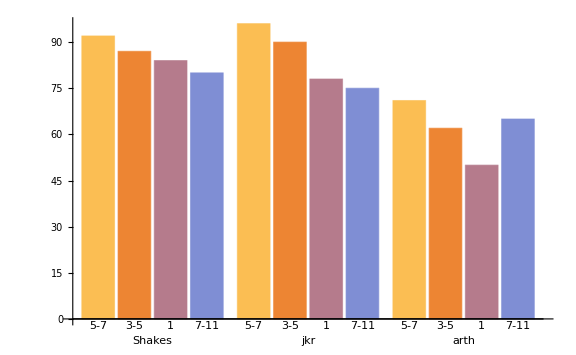

```mathematica
BarChart[asoc,ChartLabels->Automatic,ImageSize->Large]
```

The above bar chart shows the results on each category (author name) and the x axis symbols show the number of words taken in as a part of a sequence used to identify the author name.

The above bar chart shows the accuracy of classification when used the custom classifier. We can see that the accuracy is pretty high for Shakespeare and JK Rowling but it is pretty low for Arthur Conan Doyle. The primary reason fro the same is that the data of Sir Arthur Conan Doyle was lesser than the above 2. The type of text by Arthur Conan Doyle is also not very distinguishable when taken a couple of words at a time. Whereas the networks are able to classify the first 2 without any issues.

```mathematica
resultCustom2
```

{Result}

```mathematica
GraphicsRow[{PieChart[resultCustom[[2]],PlotLabel->"Performance for each Author",ColorFunction->"Rainbow"],PieChart[resultCustom[[3]]],PieChart[resultCustom[[4]]]}]
```

-Graphics-

From the above chart we can see that the classifier is pretty accurate for Shakespeare and JK Rowling but not so great for Sir Arthur Conan Doyle.

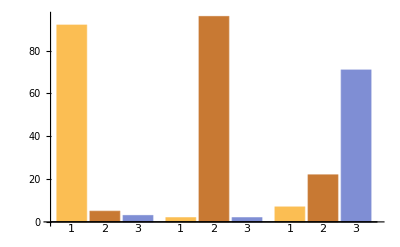

```mathematica
BarChart[resultCustom[[2;;4]],ChartLabels->{1,2,3}]
```

This shows similar result as shown above. (for 5-7 word input)

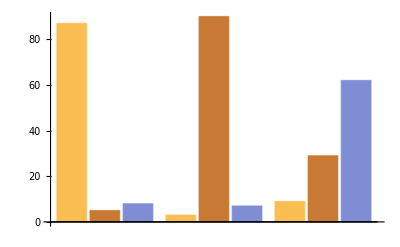

```mathematica
BarChart[resultCustom1[[2;;4]]]
```

This shows similar result as shown above. (for 3-5 word input)

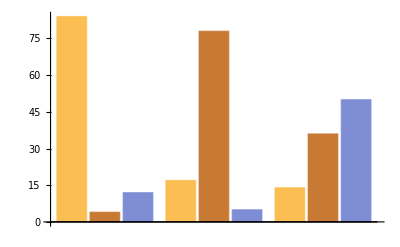

```mathematica
BarChart[resultCustom2[[2;;4]]]
```

This shows similar result as shown above. (for 1 word input)

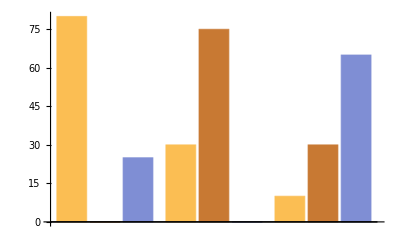

```mathematica
BarChart[resultCustom3[[2;;4]]*5]
```

This shows similar result as shown above. (for 7 - 11 word input)

The above shown are the final results.

## Future Works:

#### We could perform further test in which we could try performing the above functions without stemming (I tried it before and it was giving just as good result). We should increase the amount of training and testing data. We can also try making new neural networks which could perform better than the above ones. We can also try to use more features such as NER (named entity recognition), use of punctuation marks to improve our model. Apart from this we can use GloVe with a larger number of dimensions. We can add more number of books and authors to make this a better network. As we add the number of authors, we need to increase the number of layers in our neural network, as the number of layers. The number of neurons should be proportional to the input size.

## References and Bibliography:

#### https://web.stanford.edu/class/archive/cs/cs224n/cs224n.1174/reports/2760185.pdf https://towardsdatascience.com/decision-tree-classification-de64fc4d5aac http://www.davidsbatista.net/blog/2018/03/31/SentenceClassificationConvNets/ https://www.researchgate.net/publication/222575103_Author_identification_Using_text_sampling_to_handle_the_class_imbalance_problem https://reference.wolfram.com/language/ref/ https://reference.wolfram.com/language/ref/WordStem.html